```mathematica
answers=Import["/home/chris/Documents/tensorflow/catsVsDogs/myIntAnswers.csv","CSV"]
```

{{1,0.999985},{10,3.08474×10^-12},{100,0.000723208},{1000,0.999986},{10000,0.999513},{10001,0.0163292},12488,{9994,9.54748×10^-11},{9995,0.000743094},{9996,0.977333},{9997,0.999945},{9998,1.73922×10^-6},{9999,0.111413}}
 |  |  |  |

```mathematica
myIntAnswers=Sort[%]
```

{{1,0.999985},{2,0.999872},{3,0.999999},{4,1.},{5,6.36266×10^-12},{6,1.29628×10^-11},{7,5.91449×10^-21},12487,{12495,2.11508×10^-7},{12496,7.26232×10^-6},{12497,0.0000146436},{12498,1.},{12499,0.998803},{12500,7.01965×10^-8}}
 |  |  |  |

```mathematica
first100={};
For[i=1,i≤100,i++,
If[myIntAnswers[[i,2]]>0.5,AppendTo[first100,1],AppendTo[first100,0]]
]
Print[first100]
```

{1,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,1,0,1,1,1,1,1,0,0,1,1,1,1,0,0,0,0,0,1,0,0,1,1,1,0,1,0,1,1,0,0,0,0,0,0,0,1,0,1,1,0,1,0,1,1,1,1,0,1,1,1,1,1,1,0,1,1,1,1,0,1,0,1,0,1,1,1,1,0,1,0,0,0,1,1,0,1,1,0,0}

```mathematica
rightans=Characters["1111000000010000110010110110011110000010111101011000000110100100111011111101111000101111000001101100"]
```

{1,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,1,1,0,0,1,0,1,1,0,1,1,0,0,1,1,1,1,0,0,0,0,0,1,0,1,1,1,1,0,1,0,1,1,0,0,0,0,0,0,1,1,0,1,0,0,1,0,0,1,1,1,0,1,1,1,1,1,1,0,1,1,1,1,0,0,0,1,0,1,1,1,1,0,0,0,0,0,1,1,0,1,1,0,0}

```mathematica
numRight=0;
For[i=1,i≤100,i++,
If[rightans[[i]]==ToString[first100[[i]]],numRight++];
If[i==100,Print[numRight]]
]
```

92

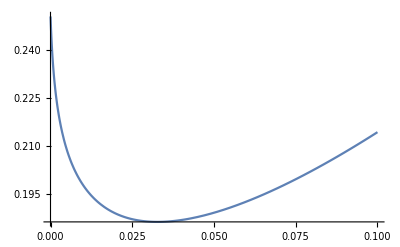

```mathematica
Plot[-1/Length[rightans]Sum[ToExpression[rightans[[i]]]Log[(1-2ϵ)*myIntAnswers[[i,2]]+ϵ]+(1-ToExpression[rightans[[i]]])Log[1-((1-2ϵ)*myIntAnswers[[i,2]]+ϵ)],{i,1,Length[rightans]}],{ϵ,0.00001,0.1}]
```

```mathematica
newMyResults=Table[{myIntAnswers[[i,1]],(1-2ϵ)*myIntAnswers[[i,2]]+ϵ/.ϵ->0.02},{i,1,Length[myIntAnswers]}]
```

{{1,0.97972},{2,0.979999},{3,0.98},{4,0.98},{5,0.0200053},{6,0.0322348},{7,0.02},{8,0.832953},{9,0.02},{10,0.02},{11,0.02},{12,0.979809},{13,0.020532},{14,0.0200246},{15,0.02},{16,0.0200767},12468,{12485,0.02},{12486,0.98},{12487,0.979992},{12488,0.977996},{12489,0.97818},{12490,0.979995},{12491,0.979983},{12492,0.97951},{12493,0.979673},{12494,0.979998},{12495,0.02},{12496,0.02},{12497,0.0200346},{12498,0.98},{12499,0.98},{12500,0.02001}}
 |  |  |  |

```mathematica
PrependTo[newMyResults,{"id","label"}]
```

{{id,label},{1,0.97972},{2,0.979999},{3,0.98},{4,0.98},{5,0.0200053},{6,0.0322348},{7,0.02},{8,0.832953},{9,0.02},{10,0.02},{11,0.02},{12,0.979809},{13,0.020532},{14,0.0200246},{15,0.02},12469,{12485,0.02},{12486,0.98},{12487,0.979992},{12488,0.977996},{12489,0.97818},{12490,0.979995},{12491,0.979983},{12492,0.97951},{12493,0.979673},{12494,0.979998},{12495,0.02},{12496,0.02},{12497,0.0200346},{12498,0.98},{12499,0.98},{12500,0.02001}}
 |  |  |  |

```mathematica
Export["/home/chris/Documents/tensorflow/catsVsDogs/myAnswers.csv",newMyResults,"CSV"]
```

/home/chris/Documents/tensorflow/catsVsDogs/myAnswers7.csv